```mathematica
testEuroValues = Import[NotebookDirectory[]<>"NEUcurve-eurs-vlarge-random.csv"][[All,1]];
```

```mathematica
initialReward = 6.5`36
capNEU = 1500000000`36
cutoffEur = 8300000000`36
limit = 2100000000`36
cumulativeExpNEU = Function[eur, (1 - Exp[-initialReward* (eur)/capNEU])*capNEU]
```

6.5

1.5×10^9

8.3×10^9

2.1×10^9

Function[eur,(1-Exp[-(initialReward eur)/capNEU]) capNEU]

```mathematica
cumulativeLinearNEU = Function[{eur,limit},cumulativeExpNEU[limit]+(capNEU - cumulativeExpNEU[limit])*(eur-limit)/(cutoffEur-limit)]
```

Function[{eur,limit},cumulativeExpNEU[limit]+((capNEU-cumulativeExpNEU[limit]) (eur-limit))/(cutoffEur-limit)]

```mathematica
cumulativeNEU = Function[{eur,limit}, Piecewise[{{cumulativeLinearNEU[eur,limit],eur≥limit  && eur <= cutoffEur},{ cumulativeExpNEU[eur], eur < limit}, {capNEU, True}}]]
```

Function[{eur,limit},Piecewise[{{cumulativeLinearNEU[eur,limit], eur≥limit&&eur≤cutoffEur}, {cumulativeExpNEU[eur], eur<limit}, {capNEU, True}}]]

```mathematica
expectedNeumarksWeis = Function[eur,{eur,cumulativeNEU[eur, limit]}] /@testEuroValues;
```

```mathematica
Export[NotebookDirectory[]<>"NEUcurve-points-random-vlarge-weis.csv", expectedNeumarksWeis]
```

C:\projects\blockchain\btc-model\NEUcurve-points-random-vlarge-weis.csv

```mathematica
Function[range,RandomReal[range, WorkingPrecision->36]&/@Range[300]]/@{{0.00000001`36,10000`36},{100000`36,10000000`36},{10000000`36,600000000`36},{600000000`36,2100000000`36},{2100000000`36,10000000000`36}};
```

```mathematica
eurosRandom=Insert[Sort[ Flatten[%]],0,1];
```

```mathematica
(*Export[NotebookDirectory[]<>"NEUcurve-eurs-vlarge-random.csv", eurosRandom]*)
```

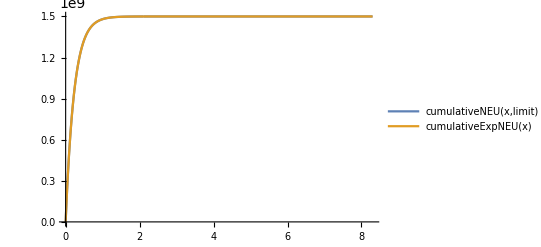

```mathematica
Plot[{cumulativeNEU[x, limit],cumulativeExpNEU[x]}, {x,0,cutoffEur}, PlotRange->All, PlotLegends->"Expressions"]
```

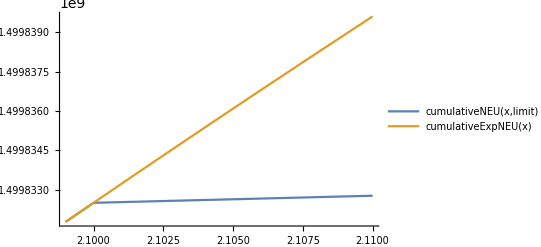

```mathematica
Plot[{cumulativeNEU[x, limit],cumulativeExpNEU[x]}, {x,limit-1000000,limit+10000000}, PlotLegends->"Expressions"]
```

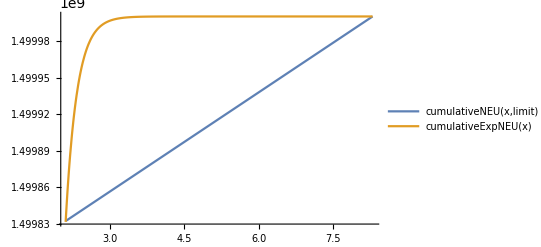

```mathematica
Plot[{cumulativeNEU[x, limit],cumulativeExpNEU[x]}, {x,limit-1000000,cutoffEur}, PlotLegends->"Expressions"]
```

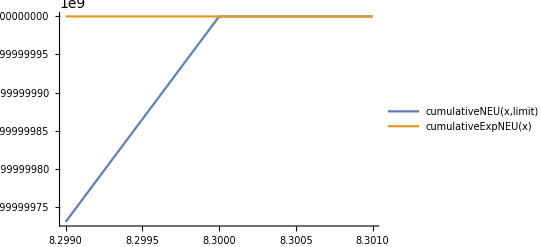

```mathematica
Plot[{cumulativeNEU[x, limit],cumulativeExpNEU[x]}, {x,cutoffEur-1000000,cutoffEur+1000000}, PlotLegends->"Expressions"]
```

```mathematica
Reap[Sow[RandomReal[{0,1}, WorkingPrecision->36]]]
```

{0.139873374691264451663286778683956165,{{0.139873374691264451663286778683956165}}}

```mathematica
(*Export[NotebookDirectory[]<>"NEUcurve-eurs.csv", testEuroValues[[All,1]]]*)
```

```mathematica
8300000000000000000000000000/10^18
```

8300000000

```mathematica
cumulativeLinearNEU[8299999999, limit]
```

1.4999999999999729840785911012736355×10^9

```mathematica
cumulativeExpNEU[2099999999.999999]
```

1.49983×10^9

```mathematica
cumulativeExpNEU[limit]
```

1.4998325012872648278965398719357334×10^9

```mathematica
cumulativeLinearNEU[cutoffEur, limit]
```

1.5×10^9

```mathematica
cumulativeLinearNEU[limit, limit]
```

1.4998325012872648278965398719357334×10^9

```mathematica
%%-%
```

167498.7127351721034601280642666

```mathematica
%/(cutoffEur - limit)
```

0.00002701592140889872636453678455912